# Sample plot

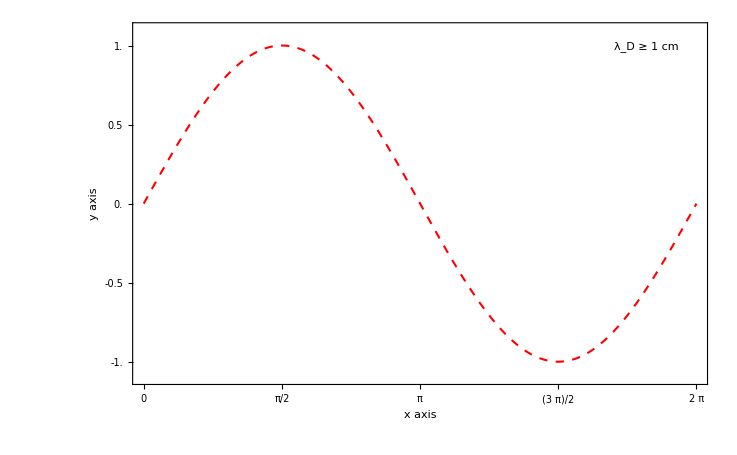

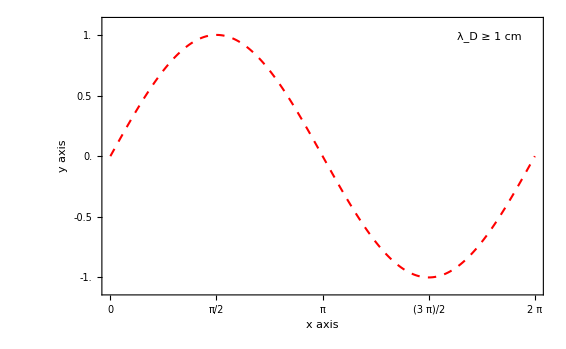

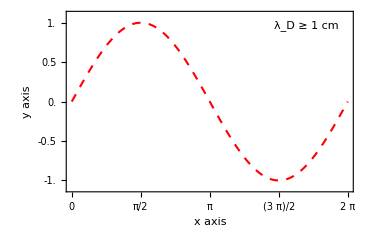

```mathematica
dt=Table[{i,Sin[i]},{i,0,2π,π/100}];
gf=ListLinePlot[

dt,

Epilog->{
(* panel label *)
Text[Style["a",{FontColor->Black,FontSize->11*2,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
(* label criteria *)
{Text[Framed[Style["λ_D ≥ 1 cm",{FontColor->Black,FontSize->9*2,FontWeight->Plain}],Background->Transparent,FrameStyle->Directive[Black,AbsoluteThickness[1]]],
Scaled[{.95,.95}],{1,1}]}
},

Joined->True,
PlotRange->{{0,2π},{-1.1,1.1}},
PlotRangePadding->0,

PlotStyle->{
{Red,AbsoluteThickness[1.5],AbsoluteDashing[6]}
},

Axes->False,
Frame->True,
FrameLabel->{{"y axis",None},{"x axis",None}},
FrameTicks->{
{Table[{i,i,{.015,0}},{i,-1,1,.5}],Table[{i,Null,{.015,0}},{i,-1,1,.5}]},
{Table[{i,i,{.015,0}},{i,0,2π,π/2}],Table[{i,Null,{.015,0}},{i,0,2π,π/2}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->9*2,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
ImageSize->(130*2)*(72/25.4),
AspectRatio->1/GoldenRatio

];

(* -- 130 mm width -- *)
gf1=Show[gf,ImageSize->(130*2)*(72/25.4)];
Print[gf1];
Export[NotebookDirectory[]<>"sample_130.pdf",gf1];

(* -- 100 mm width -- *)
gf2=Show[gf,ImageSize->(100*2)*(72/25.4)];
Print[gf2];
Export[NotebookDirectory[]<>"sample_100.pdf",gf2];

(* -- 65 mm width -- *)
gf3=Show[gf,ImageSize->(65*2)*(72/25.4)];
Print[gf3];
Export[NotebookDirectory[]<>"sample_65.pdf",gf3];
```